## 22.04.30 - 23:07 ◼ v1.1 ◼ M. J. Steil ◼ msteil@theorie.ikp.physik.tu-darmstadt.de ◼ TU Darmstadt

Initialization

```mathematica
Clear["Global`*"]

SetDirectory[NotebookDirectory[]];
SetOptions[InputNotebook[],PrivateNotebookOptions->{"FileOutlineCache"->False},TrackCellChangeTimes->False]

Get["GR.m"]
```

## Kerr metric in Boyer-Lindquist coordinates

ds^2=-dt^2+Σ/F[r]dr^2+Σ dθ^2+(r^2+a^2)Sin[θ]^2 dϕ^2+Z[r]/Σ(dt-a Sin[θ]^2 dϕ)^2; [Saul A Teukolsky 2015 Class.Quantum Grav.32 12400]
Σ[r,θ]=r^2+a^2 Cos[θ]^2

```mathematica
q={t,r,θ,ϕ};
dq={dt,dr,dθ,dϕ};
gdd`M=DiagonalMatrix[{-1,Σ[r,θ]/F[r],Σ[r,θ],(r^2+a^2)Sin[θ]^2}]+Z[r]/Σ[r,θ]*Normal@SparseArray[{{1,4}->-a Sin[θ]^2,{4,1}->-a Sin[θ]^2,{1,1}->1,{4,4}->a^2 Sin[θ]^4}]
guu`M=Inverse[gdd`M];
{dg`f,ddg`f}=Dg[gdd`M,q];

Sum[gdd`M[[μ,ν]]dq[[μ]]dq[[ν]],{μ,1,4},{ν,1,4}]//Expand
Collect[%,{dt^2,dr^2,dθ^2,dϕ^2,dt dϕ},Simplify]
```

{{-1+Z[r]/Σ[r,θ],0,0,-(a Sin[θ]^2 Z[r])/Σ[r,θ]},{0,Σ[r,θ]/F[r],0,0},{0,0,Σ[r,θ],0},{-(a Sin[θ]^2 Z[r])/Σ[r,θ],0,0,(a^2+r^2) Sin[θ]^2+(a^2 Sin[θ]^4 Z[r])/Σ[r,θ]}}

-dt^2+a^2 dϕ^2 Sin[θ]^2+dϕ^2 r^2 Sin[θ]^2+(dt^2 Z[r])/Σ[r,θ]-(2 a dt dϕ Sin[θ]^2 Z[r])/Σ[r,θ]+(a^2 dϕ^2 Sin[θ]^4 Z[r])/Σ[r,θ]+dθ^2 Σ[r,θ]+(dr^2 Σ[r,θ])/F[r]

dt^2 (-1+Z[r]/Σ[r,θ])+dϕ^2 Sin[θ]^2 (a^2+r^2+(a^2 Sin[θ]^2 Z[r])/Σ[r,θ])-(2 a dt dϕ Sin[θ]^2 Z[r])/Σ[r,θ]+dθ^2 Σ[r,θ]+(dr^2 Σ[r,θ])/F[r]

```mathematica
q={t,r,x,ϕ};(*Cos[θ]^2->x*)
dq={dt,dr,dx,dϕ};
gdd`M=DiagonalMatrix[{-1,Σ[r,θ]/F[r],Σ[r,θ]/(4 x(1−x)),(r^2+a^2)(1−x)}]+Z[r]/Σ[r,θ]*Normal@SparseArray[{{1,4}->-a (1−x),{4,1}->-a (1−x),{1,1}->1,{4,4}->a^2(1−x)^2}]/.Σ[r,θ]->r^2+a^2 x
guu`M=Inverse[gdd`M];
{dg`f,ddg`f}=Dg[gdd`M,q];

Sum[gdd`M[[μ,ν]]dq[[μ]]dq[[ν]],{μ,1,4},{ν,1,4}]//Expand
Collect[%,{dt^2,dr^2,dθ^2,dϕ^2,dt dϕ},Simplify]
```

{{-1+Z[r]/(r^2+a^2 x),0,0,-(a (1-x) Z[r])/(r^2+a^2 x)},{0,(r^2+a^2 x)/F[r],0,0},{0,0,(r^2+a^2 x)/(4 (1-x) x),0},{-(a (1-x) Z[r])/(r^2+a^2 x),0,0,(a^2+r^2) (1-x)+(a^2 (1-x)^2 Z[r])/(r^2+a^2 x)}}

-dt^2+a^2 dϕ^2+dϕ^2 r^2+(a^2 dx^2)/(4 (1-x))+(dx^2 r^2)/(4 (1-x) x)-a^2 dϕ^2 x-dϕ^2 r^2 x+(dr^2 r^2)/F[r]+(a^2 dr^2 x)/F[r]+(dt^2 Z[r])/(r^2+a^2 x)-(2 a dt dϕ Z[r])/(r^2+a^2 x)+(a^2 dϕ^2 Z[r])/(r^2+a^2 x)+(2 a dt dϕ x Z[r])/(r^2+a^2 x)-(2 a^2 dϕ^2 x Z[r])/(r^2+a^2 x)+(a^2 dϕ^2 x^2 Z[r])/(r^2+a^2 x)

-(dx^2 (r^2+a^2 x))/(4 (-1+x) x)+(dr^2 (r^2+a^2 x))/F[r]+(2 a dt dϕ (-1+x) Z[r])/(r^2+a^2 x)-(dϕ^2 (-1+x) ((a^2+r^2) (r^2+a^2 x)-a^2 (-1+x) Z[r]))/(r^2+a^2 x)+dt^2 (-1+Z[r]/(r^2+a^2 x))

```mathematica
Γ2`f=Γ2[dg`f,guu`M];
```

```mathematica
M3@Γ2`f//Simplify//MatrixForm
Γ2`print[Γ2`f,4][[All,{3,2}]]//TableForm
```

((0
-((a^2+r^2) (-2 r Z[r]+(r^2+a^2 x) Z'[r]))/(2 (r^2+a^2 x)^2 (a^2+r^2-Z[r]))
(a^2 Z[r])/(2 (r^2+a^2 x)^2)
0) | (-((a^2+r^2) (-2 r Z[r]+(r^2+a^2 x) Z'[r]))/(2 (r^2+a^2 x)^2 (a^2+r^2-Z[r]))
0
0
-(a (-1+x) (-2 (2 r^3+a^2 r (1+x)) Z[r]+(a^2+r^2) (r^2+a^2 x) Z'[r]))/(2 (r^2+a^2 x)^2 (a^2+r^2-Z[r]))) | ((a^2 Z[r])/(2 (r^2+a^2 x)^2)
0
0
(a^3 (-1+x) Z[r])/(2 (r^2+a^2 x)^2)) | (0
-(a (-1+x) (-2 (2 r^3+a^2 r (1+x)) Z[r]+(a^2+r^2) (r^2+a^2 x) Z'[r]))/(2 (r^2+a^2 x)^2 (a^2+r^2-Z[r]))
(a^3 (-1+x) Z[r])/(2 (r^2+a^2 x)^2)
0)
(-(F[r] (-2 r Z[r]+(r^2+a^2 x) Z'[r]))/(2 (r^2+a^2 x)^3)
0
0
-(a (-1+x) F[r] (-2 r Z[r]+(r^2+a^2 x) Z'[r]))/(2 (r^2+a^2 x)^3)) | (0
r/(r^2+a^2 x)-F'[r]/(2 F[r])
a^2/(2 (r^2+a^2 x))
0) | (0
a^2/(2 (r^2+a^2 x))
(r F[r])/(4 (-1+x) x (r^2+a^2 x))
0) | (-(a (-1+x) F[r] (-2 r Z[r]+(r^2+a^2 x) Z'[r]))/(2 (r^2+a^2 x)^3)
0
0
((-1+x) F[r] (2 a^2 r (-1+x) Z[r]+(r^2+a^2 x) (2 (r^3+a^2 r x)-a^2 (-1+x) Z'[r])))/(2 (r^2+a^2 x)^3))
(-(2 a^2 (-1+x) x Z[r])/((r^2+a^2 x)^3)
0
0
(2 a (a^2+r^2) (-1+x) x Z[r])/((r^2+a^2 x)^3)) | (0
(2 a^2 (-1+x) x)/((r^2+a^2 x) F[r])
r/(r^2+a^2 x)
0) | (0
r/(r^2+a^2 x)
(r^2 (1-2 x)-a^2 x^2)/(2 (-1+x) x (r^2+a^2 x))
0) | ((2 a (a^2+r^2) (-1+x) x Z[r])/((r^2+a^2 x)^3)
0
0
(2 (1-x) x (a^2+r^2-(a^2 (-1+x) (2 r^2+a^2 (1+x)) Z[r])/((r^2+a^2 x)^2)))/(r^2+a^2 x))
(0
(2 a r Z[r]-a (r^2+a^2 x) Z'[r])/(2 (r^2+a^2 x)^2 (a^2+r^2-Z[r]))
-(a Z[r])/(2 (-1+x) (r^2+a^2 x)^2)
0) | ((2 a r Z[r]-a (r^2+a^2 x) Z'[r])/(2 (r^2+a^2 x)^2 (a^2+r^2-Z[r]))
0
0
(-2 r (a^2+r^2) Z[r]+(r^2+a^2 x) (2 (r^3+a^2 r x)-a^2 (-1+x) Z'[r]))/(2 (r^2+a^2 x)^2 (a^2+r^2-Z[r]))) | (-(a Z[r])/(2 (-1+x) (r^2+a^2 x)^2)
0
0
1/2 (1/(-1+x)-(a^2 Z[r])/((r^2+a^2 x)^2))) | (0
(-2 r (a^2+r^2) Z[r]+(r^2+a^2 x) (2 (r^3+a^2 r x)-a^2 (-1+x) Z'[r]))/(2 (r^2+a^2 x)^2 (a^2+r^2-Z[r]))
1/2 (1/(-1+x)-(a^2 Z[r])/((r^2+a^2 x)^2))
0))

Γ_12^1=Γ_21^1= | -((a^2+r^2) (-2 r Z[r]+(r^2+a^2 x) Z'[r]))/(2 (r^2+a^2 x)^2 (a^2+r^2-Z[r]))
Γ_13^1=Γ_31^1= | (a^2 Z[r])/(2 (r^2+a^2 x)^2)
Γ_24^1=Γ_42^1= | -(a (-1+x) (-2 (2 r^3+a^2 r (1+x)) Z[r]+(a^2+r^2) (r^2+a^2 x) Z'[r]))/(2 (r^2+a^2 x)^2 (a^2+r^2-Z[r]))
Γ_34^1=Γ_43^1= | (a^3 (-1+x) Z[r])/(2 (r^2+a^2 x)^2)
Γ_11^2=Γ_11^2= | -(F[r] (-2 r Z[r]+(r^2+a^2 x) Z'[r]))/(2 (r^2+a^2 x)^3)
Γ_14^2=Γ_41^2= | -(a (-1+x) F[r] (-2 r Z[r]+(r^2+a^2 x) Z'[r]))/(2 (r^2+a^2 x)^3)
Γ_22^2=Γ_22^2= | r/(r^2+a^2 x)-F'[r]/(2 F[r])
Γ_23^2=Γ_32^2= | a^2/(2 (r^2+a^2 x))
Γ_33^2=Γ_33^2= | (r F[r])/(4 (-1+x) x (r^2+a^2 x))
Γ_44^2=Γ_44^2= | ((-1+x) F[r] (2 a^2 r (-1+x) Z[r]+(r^2+a^2 x) (2 (r^3+a^2 r x)-a^2 (-1+x) Z'[r])))/(2 (r^2+a^2 x)^3)
Γ_11^3=Γ_11^3= | -(2 a^2 (-1+x) x Z[r])/((r^2+a^2 x)^3)
Γ_14^3=Γ_41^3= | (2 a (a^2+r^2) (-1+x) x Z[r])/((r^2+a^2 x)^3)
Γ_22^3=Γ_22^3= | (2 a^2 (-1+x) x)/((r^2+a^2 x) F[r])
Γ_23^3=Γ_32^3= | r/(r^2+a^2 x)
Γ_33^3=Γ_33^3= | (r^2 (1-2 x)-a^2 x^2)/(2 (-1+x) x (r^2+a^2 x))
Γ_44^3=Γ_44^3= | (2 (1-x) x (a^2+r^2-(a^2 (-1+x) (2 r^2+a^2 (1+x)) Z[r])/((r^2+a^2 x)^2)))/(r^2+a^2 x)
Γ_12^4=Γ_21^4= | (2 a r Z[r]-a (r^2+a^2 x) Z'[r])/(2 (r^2+a^2 x)^2 (a^2+r^2-Z[r]))
Γ_13^4=Γ_31^4= | -(a Z[r])/(2 (-1+x) (r^2+a^2 x)^2)
Γ_24^4=Γ_42^4= | (-2 r (a^2+r^2) Z[r]+(r^2+a^2 x) (2 (r^3+a^2 r x)-a^2 (-1+x) Z'[r]))/(2 (r^2+a^2 x)^2 (a^2+r^2-Z[r]))
Γ_34^4=Γ_43^4= | 1/2 (1/(-1+x)-(a^2 Z[r])/((r^2+a^2 x)^2))

```mathematica
RM`M=genMRMAll[gdd`M,{dg`f,ddg`f},Γ2`f];
RM`f=RMac[RM`M];
```

```mathematica
RM`M[[2]]//Simplify//MatrixForm
RM`print[RM`M][[All,{3,2}]]//TableForm
```

((2 Z[r]^2 (2 a^4 (-1+x) x+(6 r^2-2 a^2 x) F[r]-(r^3+a^2 r x) F'[r])-(r^2+a^2 x) ((a^2+r^2) (r^2+a^2 x) F'[r] Z'[r]+F[r] (-10 r (a^2+r^2) Z'[r]+(r^2+a^2 x) Z'[r]^2+2 (a^2+r^2) (r^2+a^2 x) Z''[r]))+Z[r] (-4 a^4 (a^2+r^2) (-1+x) x+(r^2+a^2 x) F'[r] (2 r (a^2+r^2)+(r^2+a^2 x) Z'[r])+2 F[r] (2 (a^2+r^2) (-4 r^2+a^2 x)-3 (r^3+a^2 r x) Z'[r]+(r^2+a^2 x)^2 Z''[r])))/(4 (r^2+a^2 x)^3 F[r] (a^2+r^2-Z[r])) | (3 a^2 (-4 r Z[r]+(r^2+a^2 x) Z'[r]))/(4 (r^2+a^2 x)^3) | 0 | 0 | (a (-1+x) (2 Z[r]^2 (2 a^2 (a^2+r^2) x+(-6 r^2+2 a^2 x) F[r]+(r^3+a^2 r x) F'[r])+(r^2+a^2 x) ((a^2+r^2) (r^2+a^2 x) F'[r] Z'[r]+F[r] (-2 r (6 r^2+a^2 (5+x)) Z'[r]+(r^2+a^2 x) Z'[r]^2+2 (a^2+r^2) (r^2+a^2 x) Z''[r]))-Z[r] (4 a^2 (a^2+r^2)^2 x+(r^2+a^2 x) F'[r] (2 r (a^2+r^2)+(r^2+a^2 x) Z'[r])+2 F[r] (2 (-4 a^2 r^2-5 r^4+a^4 x)-3 (r^3+a^2 r x) Z'[r]+(r^2+a^2 x)^2 Z''[r]))))/(4 (r^2+a^2 x)^3 F[r] (a^2+r^2-Z[r])) | -(a (-2 r^2+a^2 (-3+x)) (-4 r Z[r]+(r^2+a^2 x) Z'[r]))/(4 (r^2+a^2 x)^3)
Null | (-2 (a^2 r^2 (1-2 x)+a^4 x (-4+3 x)+r^2 F[r]) Z[r]-2 a^2 x Z[r]^2+r (r^2+a^2 x) F[r] Z'[r])/(8 (-1+x) x (r^2+a^2 x)^3) | 0 | 0 | -(a (-r^2+a^2 (-3+2 x)) (-4 r Z[r]+(r^2+a^2 x) Z'[r]))/(4 (r^2+a^2 x)^3) | -(a ((2 (a^2+r^2) (-r^2+4 a^2 x)-2 r^2 F[r]) Z[r]-2 a^2 x Z[r]^2+r (r^2+a^2 x) F[r] Z'[r]))/(8 x (r^2+a^2 x)^3)
Null | Null | ((-1+x) (2 (a^2 (a^2+r^2) x-r^2 F[r]) Z[r]-2 a^2 x Z[r]^2+r (r^2+a^2 x) F[r] Z'[r]))/(2 (r^2+a^2 x)^3) | (4 a r Z[r]-a (r^2+a^2 x) Z'[r])/(4 (r^2+a^2 x)^2) | 0 | 0
Null | Null | Null | (2 a^2 r^2 (1-2 x)-2 a^4 x-2 (r^2-a^2 x) F[r]+(r^3+a^2 r x) F'[r])/(8 (-1+x) x (r^2+a^2 x) F[r]) | 0 | 0
Null | Null | Null | Null | -((-1+x) ((a^2+r^2-Z[r]) (-2 a^2 (-1+x) Z[r] (4 a^2 r^2 x+2 a^4 x (1+x)+(r^3+a^2 r x) F'[r])+(r^2+a^2 x)^2 (4 a^2 (a^2+r^2) x-2 (r^3+a^2 r x) F'[r]+a^2 (-1+x) F'[r] Z'[r]))+F[r] (4 a^2 (-1+x) (-3 r^2+a^2 x) Z[r]^2-2 Z[r] (-2 (-r^6+a^2 r^4 (-6+5 x)+a^6 x (1-x+x^2)+a^4 r^2 (-4+3 x+2 x^2))-3 a^2 r (-1+x) (r^2+a^2 x) Z'[r]+a^2 (-1+x) (r^2+a^2 x)^2 Z''[r])+(r^2+a^2 x) (-2 a^2 r (-1+x) (7 r^2+a^2 (5+2 x)) Z'[r]+a^2 (-1+x) (r^2+a^2 x) Z'[r]^2+2 (r^2+a^2 x) (2 (r^4-a^4 x)+a^2 (a^2+r^2) (-1+x) Z''[r])))))/(4 (r^2+a^2 x)^3 F[r] (a^2+r^2-Z[r])) | -(3 a^2 (a^2+r^2) (-1+x) (-4 r Z[r]+(r^2+a^2 x) Z'[r]))/(4 (r^2+a^2 x)^3)
Null | Null | Null | Null | Null | (2 ((a^2+r^2) (r^3+a^2 r x)^2+a^2 (a^2 r^2 (1-7 x)+r^4 (2-5 x)+a^4 (-4+x) x) Z[r]-a^4 (-1+x) x Z[r]^2)-r F[r] (2 a^2 r (-1+x) Z[r]+(r^2+a^2 x) (2 (r^3+a^2 r x)-a^2 (-1+x) Z'[r])))/(8 x (r^2+a^2 x)^3))

R_1212=-R_2112=-R_1221=R_2121(=R_1212=...) | (2 Z[r]^2 (2 a^4 (-1+x) x+(6 r^2-2 a^2 x) F[r]-(r^3+a^2 r x) F'[r])-(r^2+a^2 x) ((a^2+r^2) (r^2+a^2 x) F'[r] Z'[r]+F[r] (-10 r (a^2+r^2) Z'[r]+(r^2+a^2 x) Z'[r]^2+2 (a^2+r^2) (r^2+a^2 x) Z''[r]))+Z[r] (-4 a^4 (a^2+r^2) (-1+x) x+(r^2+a^2 x) F'[r] (2 r (a^2+r^2)+(r^2+a^2 x) Z'[r])+2 F[r] (2 (a^2+r^2) (-4 r^2+a^2 x)-3 (r^3+a^2 r x) Z'[r]+(r^2+a^2 x)^2 Z''[r])))/(4 (r^2+a^2 x)^3 F[r] (a^2+r^2-Z[r]))
R_1213=-R_2113=-R_1231=R_2131(=R_1312=...) | (3 a^2 (-4 r Z[r]+(r^2+a^2 x) Z'[r]))/(4 (r^2+a^2 x)^3)
R_1224=-R_2124=-R_1242=R_2142(=R_2412=...) | (a (-1+x) (2 Z[r]^2 (2 a^2 (a^2+r^2) x+(-6 r^2+2 a^2 x) F[r]+(r^3+a^2 r x) F'[r])+(r^2+a^2 x) ((a^2+r^2) (r^2+a^2 x) F'[r] Z'[r]+F[r] (-2 r (6 r^2+a^2 (5+x)) Z'[r]+(r^2+a^2 x) Z'[r]^2+2 (a^2+r^2) (r^2+a^2 x) Z''[r]))-Z[r] (4 a^2 (a^2+r^2)^2 x+(r^2+a^2 x) F'[r] (2 r (a^2+r^2)+(r^2+a^2 x) Z'[r])+2 F[r] (2 (-4 a^2 r^2-5 r^4+a^4 x)-3 (r^3+a^2 r x) Z'[r]+(r^2+a^2 x)^2 Z''[r]))))/(4 (r^2+a^2 x)^3 F[r] (a^2+r^2-Z[r]))
R_1234=-R_2134=-R_1243=R_2143(=R_3412=...) | -(a (-2 r^2+a^2 (-3+x)) (-4 r Z[r]+(r^2+a^2 x) Z'[r]))/(4 (r^2+a^2 x)^3)
R_1313=-R_3113=-R_1331=R_3131(=R_1313=...) | (-2 (a^2 r^2 (1-2 x)+a^4 x (-4+3 x)+r^2 F[r]) Z[r]-2 a^2 x Z[r]^2+r (r^2+a^2 x) F[r] Z'[r])/(8 (-1+x) x (r^2+a^2 x)^3)
R_1324=-R_3124=-R_1342=R_3142(=R_2413=...) | -(a (-r^2+a^2 (-3+2 x)) (-4 r Z[r]+(r^2+a^2 x) Z'[r]))/(4 (r^2+a^2 x)^3)
R_1334=-R_3134=-R_1343=R_3143(=R_3413=...) | -(a ((2 (a^2+r^2) (-r^2+4 a^2 x)-2 r^2 F[r]) Z[r]-2 a^2 x Z[r]^2+r (r^2+a^2 x) F[r] Z'[r]))/(8 x (r^2+a^2 x)^3)
R_1414=-R_4114=-R_1441=R_4141(=R_1414=...) | ((-1+x) (2 (a^2 (a^2+r^2) x-r^2 F[r]) Z[r]-2 a^2 x Z[r]^2+r (r^2+a^2 x) F[r] Z'[r]))/(2 (r^2+a^2 x)^3)
R_1423=-R_4123=-R_1432=R_4132(=R_2314=...) | (4 a r Z[r]-a (r^2+a^2 x) Z'[r])/(4 (r^2+a^2 x)^2)
R_2323=-R_3223=-R_2332=R_3232(=R_2323=...) | (2 a^2 r^2 (1-2 x)-2 a^4 x-2 (r^2-a^2 x) F[r]+(r^3+a^2 r x) F'[r])/(8 (-1+x) x (r^2+a^2 x) F[r])
R_2424=-R_4224=-R_2442=R_4242(=R_2424=...) | -((-1+x) ((a^2+r^2-Z[r]) (-2 a^2 (-1+x) Z[r] (4 a^2 r^2 x+2 a^4 x (1+x)+(r^3+a^2 r x) F'[r])+(r^2+a^2 x)^2 (4 a^2 (a^2+r^2) x-2 (r^3+a^2 r x) F'[r]+a^2 (-1+x) F'[r] Z'[r]))+F[r] (4 a^2 (-1+x) (-3 r^2+a^2 x) Z[r]^2-2 Z[r] (-2 (-r^6+a^2 r^4 (-6+5 x)+a^6 x (1-x+x^2)+a^4 r^2 (-4+3 x+2 x^2))-3 a^2 r (-1+x) (r^2+a^2 x) Z'[r]+a^2 (-1+x) (r^2+a^2 x)^2 Z''[r])+(r^2+a^2 x) (-2 a^2 r (-1+x) (7 r^2+a^2 (5+2 x)) Z'[r]+a^2 (-1+x) (r^2+a^2 x) Z'[r]^2+2 (r^2+a^2 x) (2 (r^4-a^4 x)+a^2 (a^2+r^2) (-1+x) Z''[r])))))/(4 (r^2+a^2 x)^3 F[r] (a^2+r^2-Z[r]))
R_2434=-R_4234=-R_2443=R_4243(=R_3424=...) | -(3 a^2 (a^2+r^2) (-1+x) (-4 r Z[r]+(r^2+a^2 x) Z'[r]))/(4 (r^2+a^2 x)^3)
R_3434=-R_4334=-R_3443=R_4343(=R_3434=...) | (2 ((a^2+r^2) (r^3+a^2 r x)^2+a^2 (a^2 r^2 (1-7 x)+r^4 (2-5 x)+a^4 (-4+x) x) Z[r]-a^4 (-1+x) x Z[r]^2)-r F[r] (2 a^2 r (-1+x) Z[r]+(r^2+a^2 x) (2 (r^3+a^2 r x)-a^2 (-1+x) Z'[r])))/(8 x (r^2+a^2 x)^3)

```mathematica
Ricci`f=Ricci[RM`f,guu`M];
```

```mathematica
M2@Ricci`f//Simplify//MatrixForm
```

(-(8 a^2 x Z[r]^3+2 Z[r]^2 (2 a^2 r^2 (1-5 x)+2 a^4 (-5+x) x-2 (r^2-a^2 x) F[r]+(r^3+a^2 r x) F'[r])+(r^2+a^2 x) ((a^2+r^2) (r^2+a^2 x) F'[r] Z'[r]+F[r] (2 r (-3 r^2+a^2 (-4+x)) Z'[r]+(r^2+a^2 x) Z'[r]^2+2 (a^2+r^2) (r^2+a^2 x) Z''[r]))-Z[r] (4 a^2 (a^2+r^2) (r^2 (1-3 x)+a^2 (-3+x) x)+(r^2+a^2 x) F'[r] (2 r (a^2+r^2)+(r^2+a^2 x) Z'[r])+2 F[r] (-6 a^2 r^2-4 r^4+2 a^4 x+4 a^2 r^2 x-(r^3+a^2 r x) Z'[r]+(r^2+a^2 x)^2 Z''[r])))/(4 (r^2+a^2 x)^4 (a^2+r^2-Z[r])) | 0 | 0 | -(a (-1+x) (8 a^2 x Z[r]^3+Z[r]^2 (-4 (a^2+r^2) (-r^2+5 a^2 x)-4 (r^2-a^2 x) F[r]+2 (r^3+a^2 r x) F'[r])+(r^2+a^2 x) ((a^2+r^2) (r^2+a^2 x) F'[r] Z'[r]+F[r] (-2 r (5 r^2+a^2 (4+x)) Z'[r]+(r^2+a^2 x) Z'[r]^2+2 (a^2+r^2) (r^2+a^2 x) Z''[r]))+Z[r] (4 (a^2+r^2)^2 (-r^2+3 a^2 x)-(r^2+a^2 x) F'[r] (2 r (a^2+r^2)+(r^2+a^2 x) Z'[r])-2 F[r] (-6 a^2 r^2-8 r^4+2 a^4 x-(r^3+a^2 r x) Z'[r]+(r^2+a^2 x)^2 Z''[r]))))/(4 (r^2+a^2 x)^4 (a^2+r^2-Z[r]))
0 | ((a^2+r^2-Z[r]) (4 a^2 (a^2+r^2) (a^2 x (1+x)+r^2 (-1+3 x))+Z[r] (-4 a^2 (a^2 x (1+x)+r^2 (-1+3 x))+2 (r^3+a^2 r x) F'[r])-(r^2+a^2 x) F'[r] (4 r^3+2 a^2 r (1+x)-(r^2+a^2 x) Z'[r]))+F[r] (8 a^2 r^4+8 r^6+4 a^4 r^2 (1-3 x)-4 a^6 x (1+x)-4 (r^2+a^2 x) Z[r]^2-2 r (5 r^4+a^4 x (3+2 x)+a^2 r^2 (3+7 x)) Z'[r]+(r^2+a^2 x)^2 Z'[r]^2+2 (a^2+r^2) (r^2+a^2 x)^2 Z''[r]+Z[r] (4 a^2 x (3 r^2+a^2 (2+x))+6 (r^3+a^2 r x) Z'[r]-2 (r^2+a^2 x)^2 Z''[r])))/(4 (r^2+a^2 x)^2 F[r] (a^2+r^2-Z[r])^2) | 0 | 0
0 | 0 | (-((a^2+r^2-Z[r]) (2 (r^4+a^4 x+a^2 r^2 (-1+3 x))-4 a^2 x Z[r]-(r^3+a^2 r x) F'[r]))+F[r] (2 a^4 x+2 a^2 r^2 (-1+2 x)+2 (r^2-a^2 x) Z[r]-(r^3+a^2 r x) Z'[r]))/(8 (-1+x) x (r^2+a^2 x)^2 (a^2+r^2-Z[r])) | 0
-(a (-1+x) (8 a^2 x Z[r]^3+Z[r]^2 (-4 (a^2+r^2) (-r^2+5 a^2 x)-4 (r^2-a^2 x) F[r]+2 (r^3+a^2 r x) F'[r])+(r^2+a^2 x) ((a^2+r^2) (r^2+a^2 x) F'[r] Z'[r]+F[r] (-2 r (5 r^2+a^2 (4+x)) Z'[r]+(r^2+a^2 x) Z'[r]^2+2 (a^2+r^2) (r^2+a^2 x) Z''[r]))+Z[r] (4 (a^2+r^2)^2 (-r^2+3 a^2 x)-(r^2+a^2 x) F'[r] (2 r (a^2+r^2)+(r^2+a^2 x) Z'[r])-2 F[r] (-6 a^2 r^2-8 r^4+2 a^4 x-(r^3+a^2 r x) Z'[r]+(r^2+a^2 x)^2 Z''[r]))))/(4 (r^2+a^2 x)^4 (a^2+r^2-Z[r])) | 0 | 0 | -((-1+x) ((a^2+r^2-Z[r]) (-8 a^4 (-1+x) x Z[r]^2-2 a^2 Z[r] (4 r^4 (-1+2 x)+2 a^4 x (3-2 x+x^2)+2 a^2 r^2 (-1+4 x+x^2)+r (-1+x) (r^2+a^2 x) F'[r])+(r^2+a^2 x)^2 (4 (a^2+r^2) (r^2+a^2 x)-2 (r^3+a^2 r x) F'[r]+a^2 (-1+x) F'[r] Z'[r]))+F[r] (4 a^2 (-1+x) (-r^2+a^2 x) Z[r]^2-2 Z[r] (-2 (-r^6+a^2 r^4 (-6+5 x)+a^6 x (1-x+x^2)+a^4 r^2 (-3+x+3 x^2))-a^2 r (-1+x) (r^2+a^2 x) Z'[r]+a^2 (-1+x) (r^2+a^2 x)^2 Z''[r])+(r^2+a^2 x) (2 r (r^4+a^2 r^2 (7-5 x)-a^4 (-4+x+2 x^2)) Z'[r]+a^2 (-1+x) (r^2+a^2 x) Z'[r]^2+2 a^2 (r^2+a^2 x) (-2 (r^2+a^2 x)+(a^2+r^2) (-1+x) Z''[r])))))/(4 (r^2+a^2 x)^4 (a^2+r^2-Z[r])))

```mathematica
R`S=R[Ricci`f,guu`M]//Simplify
```

1/(2 (r^2+a^2 x)^3 (a^2+r^2-Z[r])^2)((a^2+r^2-Z[r]) (4 (a^2+r^2) (r^4+a^4 x (1+x)+a^2 r^2 (-1+4 x))+4 a^2 x Z[r]^2+Z[r] (-4 (r^4+a^4 x (2+x)+a^2 r^2 (-1+5 x))+2 (r^3+a^2 r x) F'[r])-(r^2+a^2 x) F'[r] (4 r^3+2 a^2 r (1+x)-(r^2+a^2 x) Z'[r]))+F[r] (-4 (-r^6+a^2 r^4 (-1+x)+a^6 x (1+x)+a^4 r^2 (-1+4 x))-4 a^2 x Z[r]^2-2 r (3 r^4+a^4 x (1+2 x)+a^2 r^2 (1+5 x)) Z'[r]+(r^2+a^2 x)^2 Z'[r]^2+2 (a^2+r^2) (r^2+a^2 x)^2 Z''[r]-2 Z[r] (-2 a^2 (a^2 x (2+x)+r^2 (-1+4 x))-(r^3+a^2 r x) Z'[r]+(r^2+a^2 x)^2 Z''[r])))

(((a^2+r^2-Z[r]) (-12 a^2 x Z[r]^3+4 Z[r]^2 (r^4+a^4 x (7+x)+a^2 r^2 (-2+11 x)-(r^3+a^2 r x) F'[r])-4 1 (2 r^6+a^2 r^4 (-2+13 x)+1+2 2 (1)-(2 r^5+a^4 r x (1+x)+a^2 r^3 (1+3 x)) F'[r])+(r^2+a^2 x) (4 (a^2+r^2) (r^4+a^4 x (1+x)+a^2 r^2 (-1+4 x))-(r^2+a^2 x) F'[r] (4 r^3+2 a^2 r (1+x)-a^2 (-1+x) Z'[r])))+1)/(4 (r^2+a^2 x)^4 (a^2+r^2-Z[r])^2) | 0 | 0 | -(a (-1+x) (-12 a^2 x Z[r]^4+4+Z[r] ((a^2+r^2) (4 a^2 (a^2+r^2) (a^2 x (4+x)+r^2 (1))-1)-2 F[r] (1))))/(4 (r^2+a^2 x)^4 (a^2+r^2-Z[r])^2)
0 | (-(r^4+a^2 r^2 x-1)/F[r]+(r 1)/1)/((r^2+a^2 x)^2) | 0 | 0
0 | 0 | ((a^2+r^2-Z[r]) (1)+1)/(16 3 (1)^2) | 0
-1/1 | 0 | 0 | 1)
 |  |  |  |

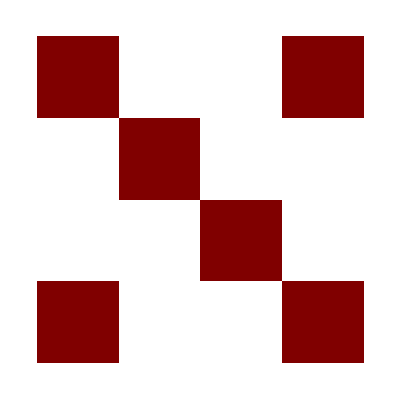

```mathematica
G`f=Ghigh[Ricci`f,R`S,gdd`M];
M2@G`f//Simplify;
%//MatrixForm
%%//ArrayPlot
```

```mathematica
G`f[2,2]//Simplify
(F[r] (a^2+r^2-Z[r]))*Numerator[%]//Together
CoefficientList[%,x]//Simplify
First@Solve[%[[2]]==0,F[r]]
0==(r-Z'[r])%%[[1]]/.%//Simplify
DSolve[%,Z[r],r]
%%%/.{%[[3,1]],D[%[[3,1]],r]}//FullSimplify//Expand
```

(-(r^4+a^2 r^2 x-a^2 x Z[r])/F[r]+(r (r Z[r]+(r^2+a^2 x) (r-Z'[r])))/(a^2+r^2-Z[r]))/((r^2+a^2 x)^2)

-a^2 r^4-r^6-a^4 r^2 x-a^2 r^4 x+r^4 F[r]+a^2 r^2 x F[r]+r^4 Z[r]+a^4 x Z[r]+2 a^2 r^2 x Z[r]+r^2 F[r] Z[r]-a^2 x Z[r]^2-r^3 F[r] Z'[r]-a^2 r x F[r] Z'[r]

{-r^4 (a^2+r^2-Z[r])+r^2 F[r] (Z[r]+r (r-Z'[r])),-a^2 ((r^2-Z[r]) (a^2+r^2-Z[r])+r F[r] (-r+Z'[r]))}

{F[r]→((r^2-Z[r]) (a^2+r^2-Z[r]))/(r (r-Z'[r]))}

r (a^2+r^2-Z[r]) Z[r] (-Z[r]+r Z'[r])==0

{{Z[r]→0},{Z[r]→a^2+r^2},{Z[r]→r C[1]}}

{F[r]→a^2+r^2-r C[1]}